# Equilibrium calculations for the hiring dynamics model Last updated: April 8, 2020 Mari Kawakatsu (Note: we can eventually turn everything into a function. For now this is just scratch work.)

## Base case: n = 2

Let' s define the base variables first:

```mathematica
n=2;(*no. of agents*)
ve=ConstantArray[1,n]; (*vector of ones*)
vzero=ConstantArray[0,n];
```

Next, define the derived variables :

```mathematica
Dout[AA_]:=DiagonalMatrix[Total[AA,{2}]]; (*row sum*)
Din[AA_]:=DiagonalMatrix[Total[AA,{1}]];(*col sum*)
L[AA_]:=Dout[AA]+Din[AA]-(AA+Transpose@AA) ;
Lα[AA_,α_]:=L[AA]+α *IdentityMatrix[n];
Λ[AA_]:=Dout[AA]-Din[AA];
```

```mathematica
γ[SS_,β_]:=Exp[β*SS]/Total[Exp[β*SS]];(*normalize*)
G[SS_,β_]:=Table[γ[SS,β],n];(*each of n rows is a copy of γ*)
```

Finally, let's define the variables that we only need in expectation:

```mathematica
EΔ[SS_,β_]:=1/n G[SS,β];
EδΛ[AA_,SS_,β_,λ_]:=(λ-1)(Λ[AA]+DiagonalMatrix[EΔ[SS,β].ve-Transpose@EΔ[SS,β].ve])
ELΔ[SS_,β_]:=DiagonalMatrix[EΔ[SS,β].ve+Transpose@EΔ[SS,β].ve]-EΔ[SS,β]-Transpose@EΔ[SS,β]
EδL[AA_,SS_,β_,λ_]:=(λ-1)(L[AA]-ELΔ[SS,β])
```

We want to solve the equation F(s) = 0.  The most general case is

```mathematica
A=Array[a,{n,n}];(*adjacenty matrix*)
S=Array[s,n];(*SpringRank vector*)
```

Just to confirm that these are what we want:

```mathematica
A //MatrixForm
S // MatrixForm
```

(a[1,1] | a[1,2]
a[2,1] | a[2,2])

(s[1]
s[2])

```mathematica
(*Λ[A].ve // MatrixForm*)
L[A] // MatrixForm
(*EΔ[S,β] // MatrixForm*)
ELΔ[S,β] // MatrixForm
(*EδΛ[A,S,β,λ].ve //FullSimplify// MatrixForm*)
EδL[A,S,β,λ]// FullSimplify// MatrixForm
```

(a[1,2]+a[2,1] | -a[1,2]-a[2,1]
-a[1,2]-a[2,1] | a[1,2]+a[2,1])

(ⅇ^(β s[1])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))+ⅇ^(β s[2])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2]))) | -ⅇ^(β s[1])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))-ⅇ^(β s[2])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))
-ⅇ^(β s[1])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))-ⅇ^(β s[2])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2]))) | ⅇ^(β s[1])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))+ⅇ^(β s[2])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2]))))

(1/2 (-1+λ) (-1+2 a[1,2]+2 a[2,1]) | -1/2 (-1+λ) (-1+2 a[1,2]+2 a[2,1])
-1/2 (-1+λ) (-1+2 a[1,2]+2 a[2,1]) | 1/2 (-1+λ) (-1+2 a[1,2]+2 a[2,1]))

```mathematica
S=FullSimplify[Inverse[Lα[A,α]].Λ[A].ve];
S // MatrixForm
S[[1]] // FullSimplify
(*S[[1]]-S[[2]] // FullSimplify*)
```

((a[1,2]-a[2,1])/(α+2 (a[1,2]+a[2,1]))
(-a[1,2]+a[2,1])/(α+2 (a[1,2]+a[2,1])))

(a[1,2]-a[2,1])/(α+2 (a[1,2]+a[2,1]))

```mathematica
EδΛ[A,S,β,λ].ve-EδL[A,S,β,λ].S // FullSimplify  // MatrixForm
```

(1/2 (-1+λ) ((2 (1+α) (a[1,2]-a[2,1]))/(α+2 (a[1,2]+a[2,1]))-Tanh[(β (a[1,2]-a[2,1]))/(α+2 (a[1,2]+a[2,1]))])
1/2 (-1+λ) (-(2 (1+α) (a[1,2]-a[2,1]))/(α+2 (a[1,2]+a[2,1]))+Tanh[(β (a[1,2]-a[2,1]))/(α+2 (a[1,2]+a[2,1]))]))

```mathematica
(*Let (a[1,2]+a[2,1])=1/2 and also divide what's inside the last set of parentheses by 2*)
sol = FindRoot[((((1+α)x)/(α+2 (1/2))-1/2 Tanh[(β x)/(α+2 (1/2))])/.{α->10^-15,β->3})==0,{x,0.5}] ;
NumberForm[sol,8]
NumberForm[(x/(1/2(α+2)))/.{α->10^-15} /.sol,8]
```

{x→0.42927982}

0.42927982

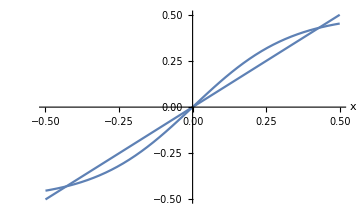

```mathematica
Plot[{((1+α) x)/((1/2)(α+2)),1/2 Tanh[(β x)/((1/2)(α+2))]}/.{α->10^-15,β->3},{x,-0.5,0.5},AxesLabel->Automatic,ImageSize->Medium]
```

## Generalization: n > 2

```mathematica
Clear[n,n1,n2]
```

Let n_1and n_2be the number of agents / departments with SpringRank scores s_1and s_2, respectively, with n_1+n_2=n.  The rows corresponding to agents with the same scores will be identical, and all elements within each row will be identical:

```mathematica
(*n1=1;n2=2;*)
(
n1=#[[1]];n2=#[[2]];
n=n1+n2;
ve=ConstantArray[1,n]; (*vector of ones*)
vzero=ConstantArray[0,n];
A=Join[ConstantArray[a1,{n,n1}],ConstantArray[a2,{n,n2}],2];(*adjacenty matrix*)
S=FullSimplify[Inverse[Lα[A,α]].Λ[A].ve];
Cond=EδΛ[A,S,β,λ].ve-EδL[A,S,β,λ].S // FullSimplify;
{Apart[Cond[[1]]*(n(a1+a2)+α)/(-1+λ)], Λ[A]//MatrixForm,n,{n1,n2} }
)&/@{{3,7}} // MatrixForm (*{{1,1},{1,2},{1,3},{2,2},{1,4},{2,3},{1,5},{2,4},{3,3},{1,6},{2,5},{3,4},{1,7},{2,6},{3,5},{4,4},{3,7}} // MatrixForm *)
```

((-14 a1-6 a2-α)/(3+7 ⅇ^((10 (a1-a2) β)/(10 (a1+a2)+α)))+1/10 (20 a2+α-70 a1 α+70 a2 α) | (-7 a1+7 a2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -7 a1+7 a2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -7 a1+7 a2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 a1-3 a2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 a1-3 a2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 a1-3 a2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 a1-3 a2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 a1-3 a2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 a1-3 a2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 a1-3 a2) | 10 | {3,7})

```mathematica
(*A=Join[ConstantArray[a,{n1,n}],ConstantArray[b,{n2,n}],1];(*adjacenty matrix*)
S=FullSimplify[Inverse[Lα[A,α]].Λ[A].ve];
Cond=EδΛ[A,S,β,λ].ve-EδL[A,S,β,λ].S // FullSimplify;
{S,Cond[[1]] } *)
```

```mathematica
sol=FindRoot[(Cond[[1]]/(-1+λ)/.{a2->(1/n-a1 n1)/n2,α->10^-15,β->3} ),{a1,0}]
Ssol=S/.{a2->1/n2(1/n-a1*n1),α->10^-15,β->3}/.sol
```

{a1→0.00105283}

{0.600992,0.600992,0.600992,-0.257568,-0.257568,-0.257568,-0.257568,-0.257568,-0.257568,-0.257568}

```mathematica
Cond/Cond[[1]]// FullSimplify
```

{1,1,1,-3/7,-3/7,-3/7,-3/7,-3/7,-3/7,-3/7}

```mathematica
Clear[n1,n2,n];

FindRoot[((2(n1 a1+n2 a2)+α)/(n2+n1*ⅇ^((n (a1-a2) β)/(n (a1+a2)+α)))+(-2a2-1/n α+n1(a1 -a2) α)/.{a2->(1/n-a1 n1)/n2,α->10^-15,β->3}/.{n->n1+n2}/.{n1->1,n2->1} ),{a1,0}]
```

{a1→0.0353601}

## More scratchwork

```mathematica
Dout[AA_]:=DiagonalMatrix[Total[AA,{2}]]; (*row sum*)
Din[AA_]:=DiagonalMatrix[Total[AA,{1}]];(*col sum*)
L[AA_]:=Dout[AA]+Din[AA]-(AA+Transpose@AA) ;
Lα[AA_,α_]:=L[AA]+α *IdentityMatrix[n];
Λ[AA_]:=Dout[AA]-Din[AA];
```

```mathematica
γ[SS_,β_]:=Exp[β*SS]/Total[Exp[β*SS]];(*normalize*)
G[SS_,β_]:=Table[γ[SS,β],n];(*each of n rows is a copy of γ*)
```

```mathematica
EΔ[SS_,β_]:=1/n G[SS,β];
EδΛ[AA_,SS_,β_,λ_]:=(λ-1)(Λ[AA]+DiagonalMatrix[EΔ[SS,β].ve-Transpose@EΔ[SS,β].ve])
ELΔ[SS_,β_]:=DiagonalMatrix[EΔ[SS,β].ve+Transpose@EΔ[SS,β].ve]-EΔ[SS,β]-Transpose@EΔ[SS,β]
EδL[AA_,SS_,β_,λ_]:=(λ-1)(L[AA]-ELΔ[SS,β])
```

```mathematica
n1=3;n2=2;
n=n1+n2;
ve=ConstantArray[1,n]; (*vector of ones*)
vzero=ConstantArray[0,n];
A=Join[ConstantArray[a1,{n,n1}],ConstantArray[a2,{n,n2}],2];(*adjacenty matrix*)

(*A // MatrixForm*)
```

```mathematica
Λ[A].ve // MatrixForm
(*Dout[A] // MatrixForm
Din[A] // MatrixForm
A + Transpose@A // MatrixForm*)
(*L[A] // MatrixForm*)
Lα[A,α] // MatrixForm
S = FullSimplify[Inverse[Lα[A,α]].Λ[A].ve];
(*ELΔ[S,β] *(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))//FullSimplify// MatrixForm*)
EδΛ[A,S,β,λ].ve/(-1+λ)// MatrixForm 
(*EδL[A,S,β,λ].S /(-1+λ) //MatrixForm*)
L[A].S //FullSimplify// MatrixForm
ELΔ[S,β].S * (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))//FullSimplify //MatrixForm
```

(-2 a1+2 a2
-2 a1+2 a2
-2 a1+2 a2
3 a1-3 a2
3 a1-3 a2)

(6 a1+2 a2+α | -2 a1 | -2 a1 | -a1-a2 | -a1-a2
-2 a1 | 6 a1+2 a2+α | -2 a1 | -a1-a2 | -a1-a2
-2 a1 | -2 a1 | 6 a1+2 a2+α | -a1-a2 | -a1-a2
-a1-a2 | -a1-a2 | -a1-a2 | 3 a1+5 a2+α | -2 a2
-a1-a2 | -a1-a2 | -a1-a2 | -2 a2 | 3 a1+5 a2+α)

(-2 a1+2 a2+(2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-(2 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))
-2 a1+2 a2+(2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-(2 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))
-2 a1+2 a2+(2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-(2 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))
3 a1-3 a2-(3 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))+(3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))
3 a1-3 a2-(3 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))+(3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))))

((10 (-a1^2+a2^2))/(5 (a1+a2)+α)
(10 (-a1^2+a2^2))/(5 (a1+a2)+α)
(10 (-a1^2+a2^2))/(5 (a1+a2)+α)
(15 (a1-a2) (a1+a2))/(5 (a1+a2)+α)
(15 (a1-a2) (a1+a2))/(5 (a1+a2)+α))

(-(2 (a1-a2) ⅇ^((2 (-a1+a2) β)/(5 (a1+a2)+α)) (1+ⅇ^((5 (a1-a2) β)/(5 (a1+a2)+α))))/(5 (a1+a2)+α)
-(2 (a1-a2) ⅇ^((2 (-a1+a2) β)/(5 (a1+a2)+α)) (1+ⅇ^((5 (a1-a2) β)/(5 (a1+a2)+α))))/(5 (a1+a2)+α)
-(2 (a1-a2) ⅇ^((2 (-a1+a2) β)/(5 (a1+a2)+α)) (1+ⅇ^((5 (a1-a2) β)/(5 (a1+a2)+α))))/(5 (a1+a2)+α)
(3 (a1-a2) ⅇ^((2 (-a1+a2) β)/(5 (a1+a2)+α)) (1+ⅇ^((5 (a1-a2) β)/(5 (a1+a2)+α))))/(5 (a1+a2)+α)
(3 (a1-a2) ⅇ^((2 (-a1+a2) β)/(5 (a1+a2)+α)) (1+ⅇ^((5 (a1-a2) β)/(5 (a1+a2)+α))))/(5 (a1+a2)+α))

```mathematica
EδΛ[A,S,β,λ].ve-(L[A].S - ELΔ[S,β].S) // MatrixForm
```

(-(6 (-a1-a2) (a1-a2))/(5 (a1+a2)+α)+(4 a1 (-2 a1+2 a2))/(5 (a1+a2)+α)-((-2 a1+2 a2) (6 a1+2 a2))/(5 (a1+a2)+α)-(4 (-2 a1+2 a2) ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))) (5 (a1+a2)+α))+(6 (a1-a2) (-ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+((-2 a1+2 a2) ((2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))+(6 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+(-2 a1+2 a2+(2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-(2 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))) (-1+λ)
-(6 (-a1-a2) (a1-a2))/(5 (a1+a2)+α)+(4 a1 (-2 a1+2 a2))/(5 (a1+a2)+α)-((-2 a1+2 a2) (6 a1+2 a2))/(5 (a1+a2)+α)-(4 (-2 a1+2 a2) ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))) (5 (a1+a2)+α))+(6 (a1-a2) (-ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+((-2 a1+2 a2) ((2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))+(6 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+(-2 a1+2 a2+(2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-(2 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))) (-1+λ)
-(6 (-a1-a2) (a1-a2))/(5 (a1+a2)+α)+(4 a1 (-2 a1+2 a2))/(5 (a1+a2)+α)-((-2 a1+2 a2) (6 a1+2 a2))/(5 (a1+a2)+α)-(4 (-2 a1+2 a2) ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))) (5 (a1+a2)+α))+(6 (a1-a2) (-ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+((-2 a1+2 a2) ((2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))+(6 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+(-2 a1+2 a2+(2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-(2 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))) (-1+λ)
(6 (a1-a2) a2)/(5 (a1+a2)+α)-(3 (-a1-a2) (-2 a1+2 a2))/(5 (a1+a2)+α)-(3 (a1-a2) (3 a1+5 a2))/(5 (a1+a2)+α)-(6 (a1-a2) ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))) (5 (a1+a2)+α))+(3 (-2 a1+2 a2) (-ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+(3 (a1-a2) (ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))/(2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))+(3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+(3 a1-3 a2-(3 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))+(3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))) (-1+λ)
(6 (a1-a2) a2)/(5 (a1+a2)+α)-(3 (-a1-a2) (-2 a1+2 a2))/(5 (a1+a2)+α)-(3 (a1-a2) (3 a1+5 a2))/(5 (a1+a2)+α)-(6 (a1-a2) ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))) (5 (a1+a2)+α))+(3 (-2 a1+2 a2) (-ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))-ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+(3 (a1-a2) (ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))/(2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))+(3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))))/(5 (a1+a2)+α)+(3 a1-3 a2-(3 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))+(3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α)))/(5 (2 ⅇ^((3 (a1-a2) β)/(5 (a1+a2)+α))+3 ⅇ^(((-2 a1+2 a2) β)/(5 (a1+a2)+α))))) (-1+λ))